```mathematica
h=10
g=1
s=1
c=4
W= B >= (c-1)(h-R *g)s+h*s
RC = R >= B/(s *g)
```

10

1

1

4

B≥10+3 (10-R)

R≥B

```mathematica
R≥B
```

R≥B

```mathematica
{5,40}
```

```mathematica
D1 =5
L1=12
D2=10
L2=1.5
T1 = {D1*Min[1,L1/(s g)],D1*L1}
T2 = {D2*Min[1,L2/(s g)],D2*L2}
ST ={FontFamily->"Latin Modern Roman 12",18,GrayLevel[0]}
OFF = {2,0}
```

5

12

10

1.5

{5,60}

{10,15.}

{FontFamily→Latin Modern Roman 12,18,GrayLevel[0]}

{2,0}

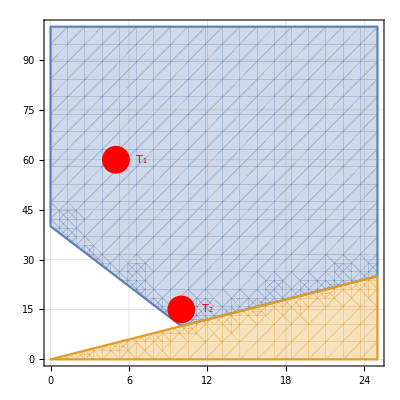

```mathematica
P = RegionPlot[Evaluate[{W && !RC,RC}],{R,0,25},{B,0,100}, GridLines->Automatic,Epilog->{PointSize[0.05],Red,Point[T1],Point[T2],Style[{Text[Subscript["T","1"], T1 + OFF],Text[Subscript["T","2"], T2 + OFF]},ST]}]
```

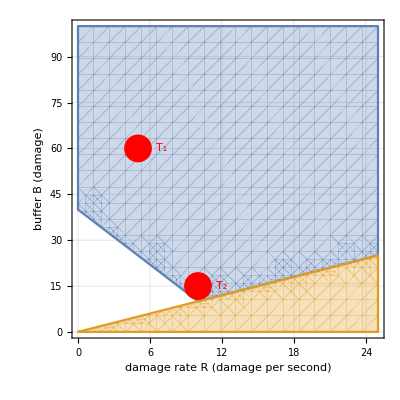

```mathematica
P2 =Show[P,FrameLabel->{{HoldForm[buffer B "(damage)"],None},{HoldForm[damage rate R "(damage per second)"],None}},PlotLabel->None,LabelStyle->ST,PlotRangePadding->0]
```